```mathematica
(*Data[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(08,12),n=10000PLANE,EM2.out"}]]
Data2[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(08,12),n=100PLANE,EM2(test).out"}]]
EM2Data[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(04,08),n=10000PLANE,EM2.out"}]]
testData:=Import[FileNameJoin[{NotebookDirectory[],"test1.out"}]]*)
IndepData:=Import[FileNameJoin[{NotebookDirectory[],"L=3,P=(04,08),n=500PLANE,EM2.out"}]]
```

```mathematica
(*data[5]=Drop[Data[5],1]/.{a_,b_,c_}:>{a,b,(1-c/10000)//N};*)
indepdata=Drop[IndepData,1]/.{{a_,b_,c_}:>{a,b,(1-c/500)//N},{}->Nothing};
(*EM2data[17]=Drop[EM2Data[17],1]/.{a_,b_,c_}:>{a,b,(1-c/10000)//N};*)
```

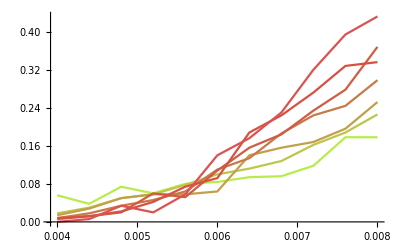

```mathematica
ListLinePlot[Map[#[[{2,3}]]&,Drop[Values@GroupBy[indepdata,First],1],{2}],PlotStyle->Table[ColorData["NeonColors"][i],{i,0,1,0.1}]]
```

```mathematica
model=NonlinearModelFit[EM2data[17],a+b(p-pt)((L+1)/2)^(1/n)+c(p-pt)^2((L+1)/2)^(2/n),{a,{pt,0.005},b,c,n},{L,p}]
```

FittedModel[0.0810114+5.67106 (1+L)^0.975951 (-0.00563684+p)+94.3675 (1+L)^1.9519 (-0.00563684+p)^2]

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0810114 | 0.00264318 | 30.6492 | 3.82683×10^-41
pt | 0.00563684 | 0.000044845 | 125.696 | 2.78964×10^-81
b | 11.1546 | 0.56365 | 19.7899 | 1.08301×10^-29
c | 365.093 | 48.0617 | 7.59634 | 1.28546×10^-10
n | 1.02464 | 0.0325604 | 31.4689 | 7.31178×10^-42

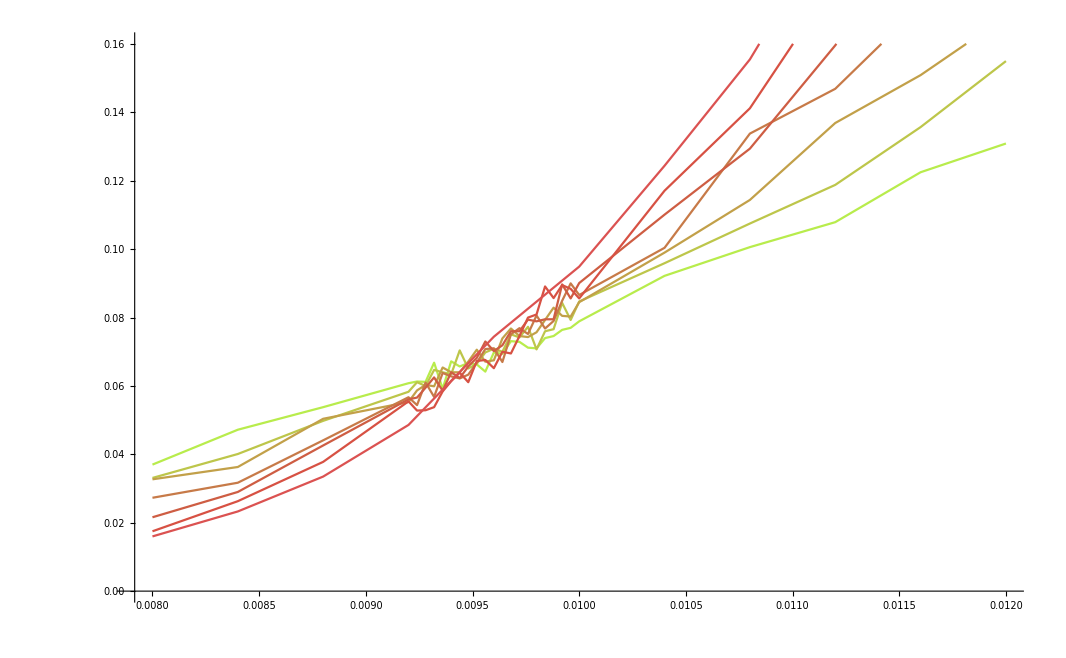

```mathematica
ListLinePlot[Map[#[[{2,3}]]&,Drop[Values@GroupBy[data[5],First],1],{2}],PlotStyle->Table[ColorData["NeonColors"][i],{i,0,1,0.1}]]
```

```mathematica
Show[(*Plot[Evaluate@Table[model[L,p],{L,3,17,2}],{p,0.025,0.032},PlotRange->{0,0.2},PlotStyle->Table[ColorData["GrayTones"][i+0.7],{i,0,1,0.1}]]*)ListLinePlot[Table[#[[{2,3}]]&/@data[17][[12i+1;;12i+11]],{i,0,6}],PlotStyle->Table[ColorData["NeonColors"][i],{i,0,1,0.1}]]]
```

Part::take: Cannot take positions 1 through 11 in data[17].

Part::partw: Part {2,3} of data[17] does not exist.

Part::partw: Part {2,3} of 1;;11 does not exist.

Part::pkspec1: The expression (1;;11)⟦{2,3}⟧ cannot be used as a part specification.

Part::take: Cannot take positions 13 through 23 in data[17].

Part::partw: Part {2,3} of data[17] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression (13;;23)⟦{2,3}⟧ cannot be used as a part specification.

Part::take: Cannot take positions 25 through 35 in data[17].

Part::pkspec1: The expression (25;;35)⟦{2,3}⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::take: Cannot take positions 37 through 47 in data[17].

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

## EM2 Data

```mathematica
data[17]
```

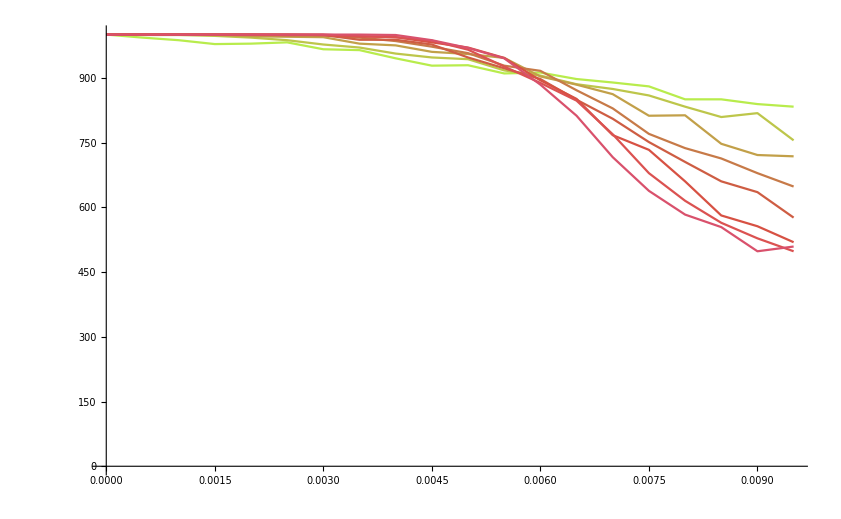

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-Cos[x]+Log[1+x]==0,x]

```mathematica
ListLinePlot[Table[#[[{2,3}]]&/@EM2Data[17][[20i+2;;20i+21]],{i,0,7}],PlotStyle->Table[ColorData["NeonColors"][i],{i,0,1,0.1}]]
```